```mathematica
Table[ShowGraph5Least[k],{k,Bases["F","AtomKeys"]}]
```

{-Graphics-034,-Graphics-1968321,-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121,-Graphics-264878,-Graphics-219519,-Graphics-204398,-Graphics-1969213,-Graphics-1968615,-Graphics-1968413,-Graphics-87579,-Graphics-72939,-Graphics-664216,-Graphics-658816,-Graphics-656215,-Graphics-29178,-Graphics-243015,-Graphics-221416,-Graphics-219016,-Graphics-97213,-Graphics-81015,-Graphics-73813,-Graphics-3338,-Graphics-2739,-Graphics-24413,-Graphics-1099,-Graphics-8416,-Graphics-3615,-Graphics-138,-Graphics-287640,-Graphics-272460,-Graphics-264885,-Graphics-227080,-Graphics-219545,-Graphics-204485,-Graphics-196965,-Graphics-94900,-Graphics-87845,-Graphics-73745,-Graphics-66705,-Graphics-31605,-Graphics-24605,-Graphics-10625,-Graphics-3640,-Graphics-295240}

```mathematica
ReverseSort[allGraphs5NullAtomKeys]
```

{59048,57528,54492,52976,52974,45416,43908,43902,40896,40878,39392,39384,39372,39368,39366,18980,17568,17514,14748,14586,13340,13284,13176,13124,13122,6320,5834,4920,4860,4428,4380,4374,2124,1944,1620,1476,1458,728,666,546,488,486,218,168,162,72,54,26,18,6,2,0}

```mathematica
Keys[allGraphs3[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
Sort[{"signature","matrix","graph","vertexsets","vertices","edges","relations","links","parents","children","comp","compwhy","colofour","colortable","colofournull","colofourrealnull"}]
```

{children,colofour,colofournull,colofourrealnull,colortable,comp,compwhy,edges,graph,links,matrix,parents,relations,signature,vertexsets,vertices}

```mathematica
Show3[k_]:=Labeled[allGraphs3[k,"graph"],{k,(ChromaticPolynomial[allGraphs3[k,"graph"],4]/4)}]
```

```mathematica
4
```

4

```mathematica
rep3=Table[allGraphs3[k,"colofournull"]->Show3[k],{k,allGraphs3FakeAtomKeys}]
```

{p1x2x3→-Graphics-{0,16},p12x3→-Graphics-{9,12},p123→-Graphics-{13,6},p13x2→-Graphics-{3,12},p1x23→-Graphics-{1,12}}

```mathematica
Table[Show3[k]->Simplify[allGraphs3[k,"colofournull"]]/.rep3,{k,Keys[allGraphs3]}]//TableForm
```

-Graphics-{0,16}→-Graphics-{0,16}
-Graphics-{9,12}→-Graphics-{9,12}
-Graphics-{12,9}→1/2 (-Graphics-{9,12}+-Graphics-{3,12}--Graphics-{1,12}+-Graphics-{13,6})
-Graphics-{13,6}→-Graphics-{13,6}
-Graphics-{14,3}→1/2 (-Graphics-{9,12}+-Graphics-{3,12}--Graphics-{1,12}--Graphics-{13,6})
-Graphics-{16,3}→1/2 (-Graphics-{9,12}--Graphics-{3,12}+-Graphics-{1,12}--Graphics-{13,6})
-Graphics-{10,9}→1/2 (-Graphics-{9,12}--Graphics-{3,12}+-Graphics-{1,12}+-Graphics-{13,6})
-Graphics-{18,4}→-Graphics-{0,16}--Graphics-{9,12}
-Graphics-{22,3}→1/2 (--Graphics-{9,12}+-Graphics-{3,12}+-Graphics-{1,12}--Graphics-{13,6})
-Graphics-{26,1}→1/2 (2 -Graphics-{0,16}--Graphics-{9,12}--Graphics-{3,12}--Graphics-{1,12}+-Graphics-{13,6})
-Graphics-{3,12}→-Graphics-{3,12}
-Graphics-{4,9}→1/2 (--Graphics-{9,12}+-Graphics-{3,12}+-Graphics-{1,12}+-Graphics-{13,6})
-Graphics-{6,4}→-Graphics-{0,16}--Graphics-{3,12}
-Graphics-{1,12}→-Graphics-{1,12}
-Graphics-{2,4}→-Graphics-{0,16}--Graphics-{1,12}

```mathematica
Table[Simplify[allGraphs5[k,"colofournull"]==0]/.RepGraph["F"],{k,alfa1s}]
```

{4 -Graphics-656124+4 -Graphics-8124+2 -Graphics-1968615+2 -Graphics-1968413+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-3615+2 -Graphics-204398+2 -Graphics-29178+2 -Graphics-2739+2 -Graphics-138+5 -Graphics-73745+5 -Graphics-66705+-Graphics-287640+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-218724+2 -Graphics-24321+2 -Graphics-921+4 -Graphics-658816+4 -Graphics-656215+4 -Graphics-81015+4 -Graphics-8416+4 -Graphics-72939+4 -Graphics-1099+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640,4 -Graphics-218724+4 -Graphics-2724+2 -Graphics-1969213+2 -Graphics-1968615+2 -Graphics-664216+2 -Graphics-656215+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+2 -Graphics-264878+2 -Graphics-72939+2 -Graphics-3338+2 -Graphics-138+5 -Graphics-87845+5 -Graphics-24605+-Graphics-227080+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-8124+2 -Graphics-121+4 -Graphics-658816+4 -Graphics-243015+4 -Graphics-219016+4 -Graphics-3615+4 -Graphics-87579+4 -Graphics-2739+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-94900+-Graphics-3640,4 -Graphics-8124+4 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-658816+2 -Graphics-656215+2 -Graphics-243015+2 -Graphics-221416+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-87579+2 -Graphics-29178+5 -Graphics-219545+5 -Graphics-73745+-Graphics-3640+-Graphics-295240==2 -Graphics-24321+2 -Graphics-2724+2 -Graphics-921+2 -Graphics-121+4 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-219016+4 -Graphics-81015+4 -Graphics-219519+4 -Graphics-72939+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900,4 -Graphics-656124+4 -Graphics-2724+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-243015+2 -Graphics-219016+2 -Graphics-81015+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+2 -Graphics-219519+2 -Graphics-29178+2 -Graphics-3338+2 -Graphics-138+5 -Graphics-87845+5 -Graphics-66705+-Graphics-272460+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-24321+2 -Graphics-324+4 -Graphics-664216+4 -Graphics-656215+4 -Graphics-221416+4 -Graphics-3615+4 -Graphics-87579+4 -Graphics-1099+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-73745+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-227080+-Graphics-94900+-Graphics-3640,4 -Graphics-218724+4 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-664216+2 -Graphics-658816+2 -Graphics-97213+2 -Graphics-81015+2 -Graphics-24413+2 -Graphics-3615+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-3338+2 -Graphics-1099+5 -Graphics-219545+5 -Graphics-24605+-Graphics-94900+-Graphics-295240==2 -Graphics-656124+2 -Graphics-72921+2 -Graphics-921+2 -Graphics-121+4 -Graphics-1968615+4 -Graphics-243015+4 -Graphics-221416+4 -Graphics-8416+4 -Graphics-219519+4 -Graphics-2739+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-3640}

```mathematica
Simplify[allGraphs5[59048,"colofournull"]==0]/.RepGraph["F"]
```

2 (12 -Graphics-034+-Graphics-1969213+-Graphics-1968615+-Graphics-1968413+-Graphics-664216+-Graphics-658816+-Graphics-656215+-Graphics-243015+-Graphics-221416+-Graphics-219016+-Graphics-97213+-Graphics-81015+-Graphics-73813+-Graphics-24413+-Graphics-8416+-Graphics-3615+-Graphics-264878+-Graphics-219519+-Graphics-204398+-Graphics-87579+-Graphics-72939+-Graphics-29178+-Graphics-3338+-Graphics-2739+-Graphics-1099+-Graphics-138)+-Graphics-295240==6 -Graphics-1968321+6 -Graphics-656124+6 -Graphics-218724+6 -Graphics-72921+6 -Graphics-24321+6 -Graphics-8124+6 -Graphics-2724+6 -Graphics-921+6 -Graphics-324+6 -Graphics-121+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640

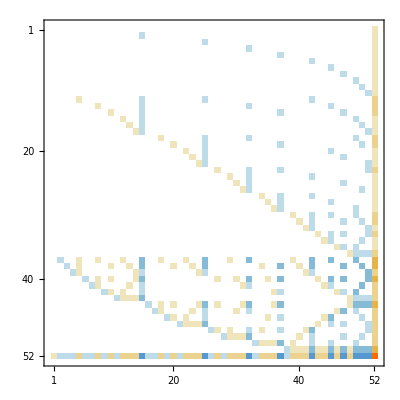

```mathematica
Map[Sign,Table[BaseCoeff[k,"F"],{k,ReverseSort[allGraphs5NullAtomKeys]}]]//PseudoInverse//MatrixPlot
```

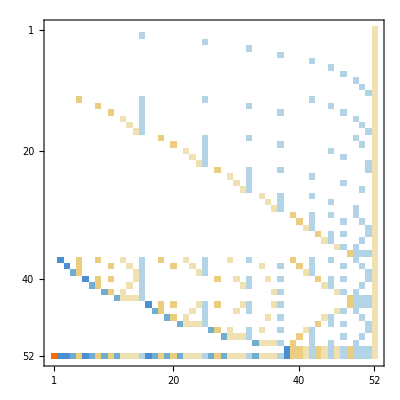

```mathematica
Table[BaseCoeff[k,"F"],{k,ReverseSort[allGraphs5NullAtomKeys]}]//PseudoInverse//MatrixPlot
```